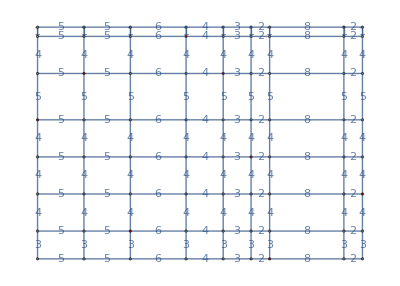

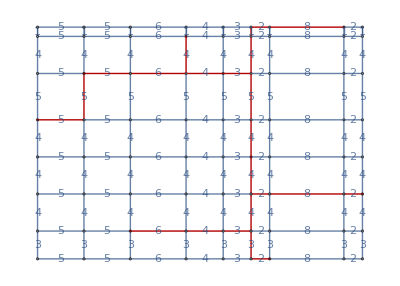
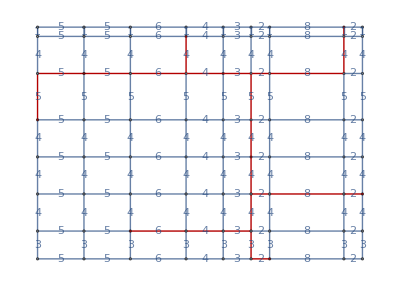
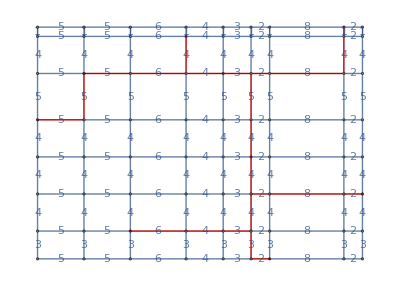
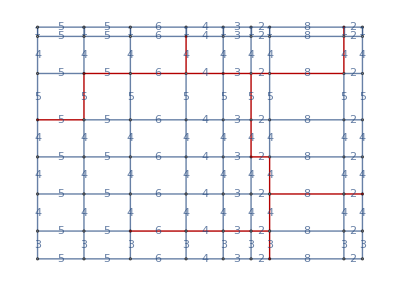
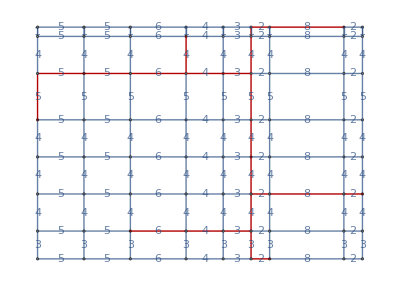
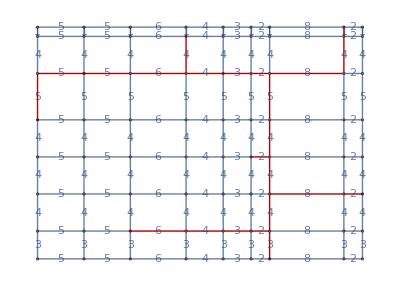
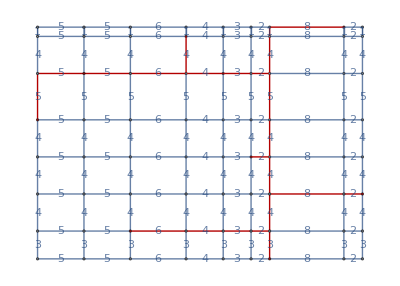
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ClearAll["Global`*"]

(*Running this notebook file generates the graphics for the trees in the directory MMFP_reduced_graphs on the hanan grid generated by points {0,15},{5,20},{16,24},{20,20},{33,25},{23,11},{35,7},{25,0},{10,3}. Editing this file will most likely break it.*)


dim=2;
vert ={{0,15},{5,20},{16,24},{20,20},{33,25},{23,11},{35,7},{25,0},{10,3}};
(*{0,15},{5,20},{16,24},{20,20},{33,25},{23,11},{35,7},{25,0},{10,3}*)

gethanangrid[vertin_]:=Module[{vert=vertin,dict},

(*Create all hanan vertices*)
hananvert = DeleteDuplicates[Distribute[Transpose[vert],List]];

(*Print["Hanan Grid vertices: ",hananvert]*)

hanandat={};

Do[
(*Initialize dictionary stucture with every point in hananvert a key*)
Map[Function[i,dict[d,i]={}],hananvert];
(*Find all (dim-d)-embeded edges*)
Map[Function[i,Map[Function[j,If[Count[MapThread[Equal,{i,j}],False]==1&&i[[d]]≠j[[d]],AppendTo[dict[d,i],j] ]],hananvert]],hananvert];
(*Reduce to adjacent edges only*)
Map[Function[key,
(*Print["dict[",d,",",key,"]: ",dict[d,key]];*)
temp=Sort[Map[Function[val,{key[[d]]-val[[d]],key, val}],dict[d,key]],#1[[1]]<#2[[1]]&];
If[temp[[1,1]]>0,AppendTo[hanandat,{UndirectedEdge[temp[[1,2]],temp[[1,3]]],Abs[temp[[1,1]]]}],
If[temp[[-1,1]]<0,AppendTo[hanandat,{UndirectedEdge[temp[[-1,2]],temp[[-1,3]]],Abs[temp[[-1,1]]]}],
pos = FirstPosition[temp,{x_ /; x>0, _, _},Null,1];
AppendTo[hanandat,{UndirectedEdge[temp[[pos,2]][[1]],temp[[pos,3]][[1]]],Abs[temp[[pos,1]][[1]]]}];
AppendTo[hanandat,{UndirectedEdge[temp[[pos-1,2]][[1]],temp[[pos-1,3]][[1]]],Abs[temp[[pos-1,1]][[1]]]}];
]
]
],Part[DownValues[dict],All,1,1,2]];
,{d,dim}];

edger=UndirectedEdge[p1_,p2_]:>UndirectedEdge[p2,p1];hanandat = DeleteDuplicates[hanandat, #1[[1]]==(#2[[1]]/.edger)||#1==#2&];

hananedges = ParallelMap[#[[1]]&,hanandat];
hananedgeweights=ParallelMap[#[[2]]&,hanandat];

(*Print[hananedges]*)

If[dim≤3,
hanang=Graph[hananvert,hananedges,VertexCoordinates->hananvert,VertexStyle->Map[#->Red&,vert],EdgeWeight->hananedgeweights,EdgeLabels->"EdgeWeight"],
hanang=Graph[hananvert,hananedges,VertexStyle->Map[#->Red&,vert],EdgeWeight->hananedgeweights]
];

hanang
]

mintreesonv[vertin_,gridin_]:=Module[{vert=vertin,grid=gridin},
MinimalBy[Parallelize[Select[Subgraph[grid,#]&/@Map[Join[vert,#]&,Subsets[Complement[VertexList[grid],vert]]],TreeGraphQ]],Length[VertexList[#]]&]
]

gunongrid[gridin_,graphsin_]:=Module[{grid=gridin,graphs=graphsin},frame=Flatten[Map[Function[graph,nedges=Complement[EdgeList[graph],EdgeList[grid]];Join[Complement[EdgeList[graph],nedges],Flatten[Map[Function[ed,Map[UndirectedEdge[#[[1]],#[[2]]]&,Subsequences[FindShortestPath[grid,ed[[1]],ed[[2]]],{2}]]],nedges],2]]],graphs],1];framegraph=Subgraph[grid,frame];Map[Function[m,PropertyValue[{framegraph,m},EdgeWeight]=PropertyValue[{wholegrid,m},EdgeWeight]],frame];framegraph]

wholegrid=gethanangrid[vert]

files=FileNames["*.m",NotebookDirectory[]<>"/MMFP_reduced_graphs"];
mintrees = Map[Function[ddfh,Import[ddfh]],files];

Parallelize[Map[HighlightGraph[wholegrid,{#}]&,mintrees]]
```